# Aula 10 - Introdução à Física Computacional I

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

No mesmo espírito do mapa logístico, estude o mapa definido por: x_(n + 1)= x_n Exp[4 λ (1 - x_n)].
Em particular, produza um diagrama de bifurcações contendo 400 valores de λ entre λ  = 0.42 e λ = 0.82. Note que os valores de  x orrespondentes aos atratores agora não estão mais restritos ao intervalo 0 ≤ x ≤ 1; uma boa escolha, dado o intervalo de valores de λ que nos interessa, é  0 ≤ x ≤ 3.
Com base no diagrama de bifurcações, determine com pelo menos 6 algarismos significativos os valores de  λ em que ocorrem as 5 primeiras bifurcações. A partir desses resultados, estime o expoente δ de Feigenbaum. O valor encontrado é compatível com o valor exato válido para máximos quadráticos (δ ≈ 4.6692)?
(Respostas:  há bifurcações em  λ = 1/2, λ = 0.631617, λ = 0.664088, λ = 0.671156, λ=0.672677 )

```mathematica
f[λ_][x_]:=x*Exp[4*λ*(1-x)]
```

```mathematica
optam={ImageSize->Large,LabelStyle->{"Large"}};
```

Gráfico de f(x), de f(f(x)) e dos “fluxos” para diversos valores de λ

```mathematica
grafmapa[λ_,x0_,n_]:=
(
xx=x0;
lista1={{xx,0},{xx,f[λ][xx]}};
Do[
(
xx=f[λ][xx];AppendTo[lista1,{xx,xx}];
AppendTo[lista1,{xx,f[λ][xx]}]),
{i,1,n}
];
grafico0=Plot[{x,f[λ][x],Nest[f[λ],x,2]},{x,0,4},Evaluate[optam],AxesLabel->{"x","f(x)"}];
Show[{grafico0,ListLinePlot[lista1,PlotStyle->Red]}]
)
```

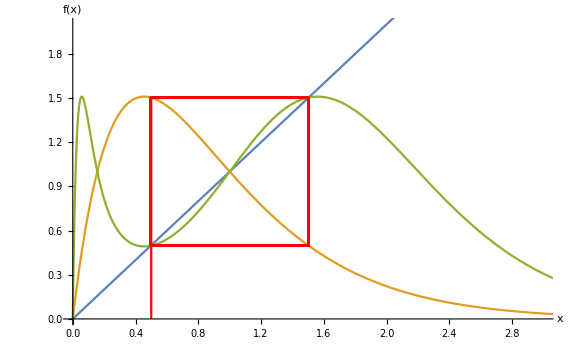

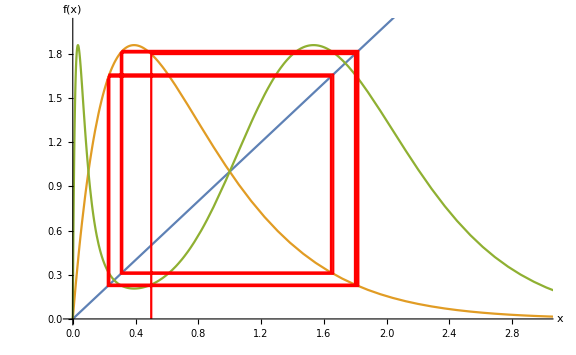

```mathematica
Show[grafmapa[0.4,0.5,10],PlotRange->{{0,3},{0,2}}]
Show[grafmapa[0.55,0.5,10],PlotRange->{{0,3},{0,2}}]
Show[grafmapa[0.64,0.5,10],PlotRange->{{0,3},{0,2}}]
```

A seguir temos o diagrama de bifurcação

```mathematica
pontos:=Compile[{λ,{m,_Integer},{n,_Integer}},
(
xlista=Drop[NestList[#*Exp[4*λ*(1-#)]&,0.5,n],m+1];
saida={};
Do[AppendTo[saida,{λ,xlista[[i]]}],{i,1,Length[xlista]}];
saida
),{{saida,_Real,2}}]
```

```mathematica
varrepontos:=Compile[{λmin,λmax,nλ,{m,_Integer},{n,_Integer}},
(
grandelista={};
Do[AppendTo[grandelista,pontos[λ,m,n]],{λ,λmin,λmax,(λmax-λmin)/nλ}];
Flatten[grandelista,1]
),{{grandelista,_Real,3}}]
```

```mathematica
diagbifurca[λmin_,λmax_,nλ_,m_,n_]:=ListPlot[varrepontos[λmin,λmax,nλ,m,n],Axes->False,Frame->True,FrameLabel->{"λ","x"},PlotStyle->PointSize[0.001],AspectRatio->1,Evaluate[optam]]
```

```mathematica
diagbifurca[0.42,0.82,800,1024,1024+512]
```

-Graphics-

```mathematica
Show[diagbifurca[0.6,0.7,500,1024,1024+512],PlotRange->{0.11,0.31}]
```

-Graphics-

```mathematica
Show[diagbifurca[0.66,0.68,500,1024,1024+512],PlotRange->{0.11,0.17}]
```

-Graphics-

Analisando a estabilidade dos diversos ciclos:

```mathematica
est1=FindRoot[{x==Nest[f[λ],x,1],D[Nest[f[λ],x,1],x]==-1},{{x,0.99},{λ,0.49}}]
```

{x→1.,λ→0.5}

```mathematica
est2=FindRoot[{x==Nest[f[λ],x,2],D[Nest[f[λ],x,2],x]==-1},{{x,0.28},{λ,0.63}}]
```

{x→0.277704,λ→0.631617}

```mathematica
est4=FindRoot[{x==Nest[f[λ],x,4],D[Nest[f[λ],x,4],x]==-1},{{x,0.15},{λ,0.66}}]
```

{x→0.154693,λ→0.664088}

```mathematica
est8=FindRoot[{x==Nest[f[λ],x,8],D[Nest[f[λ],x,8],x]==-1},{{x,0.16},{λ,0.67}}]
```

{x→0.164862,λ→0.671156}

```mathematica
est16=FindRoot[{x==Nest[f[λ],x,16],D[Nest[f[λ],x,16],x]==-1},{{x,0.17},{λ,0.673}}] (* Demora cerca de 1 min 20 s*)
```

{x→0.170075,λ→0.672677}

```mathematica
δest=((λ/. est8)-(λ/. est4))/((λ/. est16)-(λ/. est8))
```

4.64553

```mathematica
((λ/. est4)-(λ/. est2))/((λ/. est8)-(λ/. est4))
```

4.59445

```mathematica
((λ/. est2)-(λ/. est1))/((λ/. est4)-(λ/. est2))
```

4.05332